11.3 TE and TM Guided Modes using Chen’s Approach
C. Chen, P. Berini, D. Feng, S. Tanev, and V. P. Tzolov, “Efficient and accurate numerical analysis of multilayer planar optical waveguides in lossy anisotropic media,” Opt. Express, vol. 7, pp. 260–272, Oct. 2000.

```mathematica
(*========================= 初期化セル =========================*)
(*屈折率の関数を定義したノートブックを呼び出して評価*)
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
RefractiveIndexDefNotebookNames={
"Gehrsitz(2000)に基づくAlGaAsの組成比・温度・波長に依存した屈折率の導出.nb",(*nAlGaAs[(*Al組成比x*),(*温度T*),(*波長λ*)]*)
"SiO2とTiO2の室温の屈折率の導出.nb"};(*nSiO2RoomT[(*波長λ*)],nTiO2RoomT[(*波長λ*)]*)
Do[
nb=NotebookOpen[FileNameJoin[{NotebookDirectory[],RefractiveIndexDefNotebookName}]];
NotebookEvaluate[nb,EvaluationElements->"InitializationCell"];
NotebookClose[nb]
,{RefractiveIndexDefNotebookName,RefractiveIndexDefNotebookNames}]

(*DBRを構成する各層の実部の屈折率のリストを与える関数*)
DBRNList[DBRPairNum_,N1_,N2_]:=Flatten[Table[{N1,N2},DBRPairNum]]
(*実部の屈折率のリストから目標波長におけるDBRの各層の厚さのリストを与える関数*)
DBRThicknessList[RefractiveIndexList_,TargetWavelength_]:=Table[TargetWavelength/(4*Re[RefractiveIndexList[[i]]]),{i,Length[RefractiveIndexList]}]
(*任意の行列のリストからそれらすべて内積した行列を与える関数*)
ListDot[list_]:=Apply[Dot,list];(*遅い*)
(*M[1]=First[CharaMatrixList];M[n_]:=M[n]=M[n-1].CharaMatrixList[[n]]*)
ListMultiplier1[list_,partitionwidth_: 4]:=Apply[Dot,Dot@@@Partition[list,UpTo[partitionwidth]]]
ListMultiplier2[list_,partitionwidth_: 2]:=NestWhile[Dot@@@Partition[#,partitionwidth,partitionwidth,1,{}]&,list,Dimensions[#][[1]]>1&][[1]]
(*Plot画像保存用関数*)
ExpVectorImg[plot_,name_]:=Export[FileNameJoin[{NotebookDirectory[],name<>".svg"}],plot,"SVG"]
ExpBitmapImg[plot_,name_]:=Export[FileNameJoin[{NotebookDirectory[],name<>".png"}],plot,"PNG",ImageResolution-> 600]
```

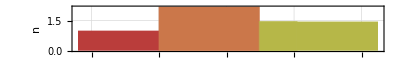

```mathematica
(*=================================================================*)
(*DBRミラーの目標波長[μm]*)TargetWL=0.81;
(*入射媒質の複素屈折率*)IncidentN=1;
(*基板媒質の複素屈折率*)SubstrateN=nSiO2RoomT[(*波長λ*)λ]/.λ-> TargetWL;
(*DBRミラーのペア数*)DBR1PairNum=5;DBR2PairNum=10;
(*DBR層の複素屈折率*)
DBRHighN=nTiO2RoomT[(*波長λ*)λ];
DBRLowN=nSiO2RoomT[(*波長λ*)λ];
(*複素屈折率のリスト*)

(*NList=Join[
(*DBRNList[DBR1PairNum,DBRHighN,DBRLowN],*){
1,
1.49,
2.1810
},
DBRNList[DBR2PairNum,DBRLowN,DBRHighN]
]/.λ-> TargetWL;;
(*各層の厚さのリスト*)
ThicknessList=Join[
(*(1/4)*(TargetWL/Re[DBRNList[DBR1PairNum,DBRHighN,DBRLowN]]),*){
3*TargetWL,
(0/4)*(TargetWL/1.49),
(2/2)*(TargetWL/2.1810)
},
(1/4)*(TargetWL/Re[DBRNList[DBR2PairNum,DBRLowN,DBRHighN]])
]/.λ-> TargetWL;*)

NList=Join[{
2.1810,
nSiO2RoomT[(*波長λ*)λ]
}
]/.λ-> TargetWL;;
(*各層の厚さのリスト*)
ThicknessList=Join[{
(2/2)*(TargetWL/2.1810),
(1/4)*(TargetWL/nSiO2RoomT[(*波長λ*)λ])
}
]/.λ-> TargetWL;
(*=================================================================*)
(*屈折率分布の可視化*)RefracIndexPlot=Show[
ListLinePlot[{{{-0.3,Re[IncidentN]},{0,Re[IncidentN]}},{{Last[Accumulate[ThicknessList]],Re[ReplaceAll[SubstrateN,λ->TargetWL] ]},{Last[Accumulate[ThicknessList]]+0.3,Re[ReplaceAll[SubstrateN,λ->TargetWL] ]}}},
PlotStyle->Directive[Opacity[0]],PlotTheme->{"Scientific","SansLabels"},Filling-> 0,FillingStyle->Automatic,ColorFunction->Function[{width,height},ColorData["DarkRainbow"][1-Mod[height,0.5]]],ColorFunctionScaling-> False],
RectangleChart[
Table[{Re[ThicknessList][[i]],ReplaceAll[Re[NList],λ->TargetWL] [[i]]},{i,Length[NList]}],
BarSpacing->None,PlotTheme->{"Scientific","SansLabels"},LabelingFunction->Automatic,ColorFunction->Function[{width,height},ColorData["DarkRainbow"][1-Mod[height,0.5]]],ColorFunctionScaling-> False
],
GridLines->Automatic,PlotRange->{0.,Automatic},PlotLabel->"Refractive index @ "<>ToString[TargetWL]<>" [μm]",FrameLabel->{"Distance from surface [μm]","n"},AspectRatio-> 1/(4*GoldenRatio),ImageSize-> Scaled[0.8]]
```

```mathematica
k[λ_,N_]:=(2π/λ)*N
γ[k0_,N_,β_]:=Sqrt[β^2-k0^2*N^2]
kxi[k0_,Ni_,β_]:=Sqrt[k0^2*Ni^2-β^2]
Mi[k_,h_]:=(*If[k==0,({{1, -h}, {0, 1}}),*)({{Cos[k h], -Sin[k h]/k}, {k*Sin[k h], Cos[k h]}})(*]*)
```

```mathematica
MiList=Table[
Mi[kxi[k[TargetWL,NList[[i]]],NList[[i]],β],ThicknessList[[i]]]
,{i,Length[ThicknessList]}];
Print["特性マトリックスの全内積計算時間:",AbsoluteTiming[
M=ListMultiplier2[MiList];
][[1]],"[s]"]
```

特性マトリックスの全内積計算時間:0.0005049[s]

```mathematica
Fte=γ[k[TargetWL,1],SubstrateN,β]*M[[2,2]]+
γ[k[TargetWL,1],IncidentN,β]*M[[1,1]]-
γ[k[TargetWL,1],SubstrateN,β]*γ[k[TargetWL,1],IncidentN,β]*M[[1,2]]-
M[[2,1]];
```

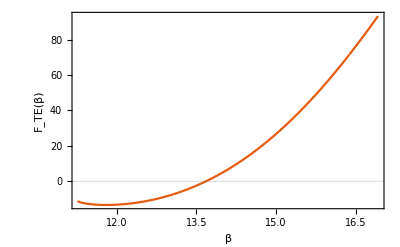

```mathematica
Plot[Fte,{β,k[TargetWL,1]*SubstrateN,k[TargetWL,1]*Max[NList]},
FrameLabel->{"β","F_TE(β)"},
PlotTheme->{(*"Monochrome",*)"Scientific","SansLabels"}]
```

```mathematica
βSolve=NSolve[Fte==0&&k[TargetWL,1]*SubstrateN<β<k[TargetWL,1]*Max[NList],β,Reals]
```

{{β→13.6828}}